```mathematica
(* names:
for Λ = 0 "rhouncert 12 balls r<30" or "rho 12 balls r<20"
for Λ positive "rhouncert 12 balls r<30 Λ=0.0001"
for Λ negative "rhouncert 12 balls r<30 negamma"

*)

(*Export["rho 56 balls r<40 Λ=0.0001.wl",interdatrho];
Export["rhouncert 56 balls r<40 Λ=0.0001.wl",uncrholist];
Export["P 56 balls r<40 Λ=0.0001.wl",interdatP];
Export["Puncert 56 balls r<40 Λ=0.0001.wl",uncPlist];*)
```

```mathematica
(*SystemOpen["P 12 balls r<20.wl"]*)
```

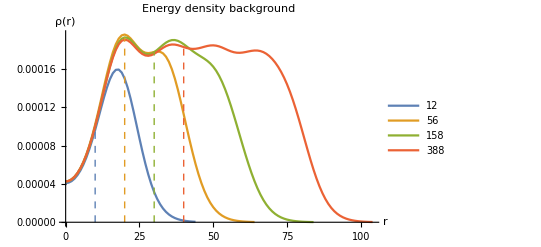

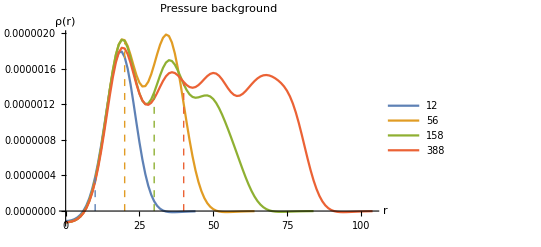

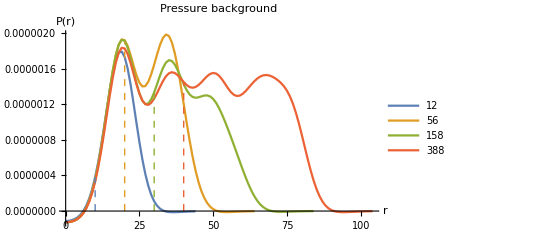

```mathematica
(*functions for plotting lines for π,P for Λ=0*)
a20f = Interpolation[a20];
a40f = Interpolation[a40];
a60f = Interpolation[a60];
a80f = Interpolation[a80];
a20p = Interpolation[b20];
a40p = Interpolation[b40];
a60p = Interpolation[b60];
a80p = Interpolation[b80];
map={"Default"->97,"Earth"->98,"Garnet"->99,"Opal"->100,"Sapphire"->101,"Steel"->102,"Sunrise"->103,"Textbook"->104,"Water"->105,"BoldColor"->106,"CoolColor"->107,"DarkColor"->108,"MarketingColor"->109,"NeonColor"->109,"PastelColor"->110,"RoyalColor"->111,"VibrantColor"->112,"WarmColor"->113};

u = a40f[20]-0.000003;
u2 = a40p[20]-0.000000025;
lineStyle1={ColorData[97,1],Dashed};
lineStyle2={ColorData[97,2],Dashed};
lineStyle3={ColorData[97,3],Dashed};
lineStyle4={ColorData[97,4],Dashed};

line1=Line[{{10,0},{10,a20f[10]}}];
line2=Line[{{20,0},{20,u}}];
line3=Line[{{30,0},{30,a60f[30]}}];
line4=Line[{{40,0},{40,a80f[40]}}];

line5=Line[{{10,0},{10,a20p[10]}}];
line6=Line[{{20,0},{20,u2}}];
line7=Line[{{30,0},{30,a60p[30]}}];
line8=Line[{{40,0},{40,a80p[40]}}];

(*Epilog->{Directive[lineStyle2],line2},Epilog->{Directive[lineStyle3],line3},Epilog->{Directive[lineStyle4],line4}*)


w20pos = Table[{a20[[i,1]],b20[[i,2]]/a20[[i,2]]},{i,1,Length[a20]}];
w40pos = Table[{a40[[i,1]],b40[[i,2]]/a40[[i,2]]},{i,1,Length[a40]}];
w60pos = Table[{a60[[i,1]],b60[[i,2]]/a60[[i,2]]},{i,1,Length[a60]}];
w80pos = Table[{a80[[i,1]],b80[[i,2]]/a80[[i,2]]},{i,1,Length[a80]}];

wpos20f = Interpolation[w20pos];
wpos40f = Interpolation[w40pos];
wpos60f = Interpolation[w60pos];
wpos80f = Interpolation[w80pos];

u = a40f[20]-0.000003;
u2 = a40p[20]-0.000000025;

line11pw=Line[{{10,0},{10,wpos20f[10]}}];
line21pw=Line[{{20,0},{20,wpos40f[20]}}];
line31pw=Line[{{30,0},{30,wpos60f[30]}}];
line41pw=Line[{{40,0},{40,wpos80f[40]}}];

ListLinePlot[{w20pos, w40pos,w60pos,w80pos},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},AxesLabel->{r,"w(r)"},PlotLabel->Style["Equation of state",12.4],PlotLegends->Placed[{"12","56","158","388"},Below],PlotRange -> {{0,100},{0,0.012}},Epilog->{{Directive[lineStyle1],line11pw},{Directive[lineStyle2],line21pw},{Directive[lineStyle3],line31pw},{Directive[lineStyle4],line41pw}}];









w20neg = Table[{ρneg20[[i,1]],Pneg20[[i,2]]/ρneg20[[i,2]]},{i,1,Length[ρneg20]-55}];
w40neg = Table[{ρneg40[[i,1]],Pneg40[[i,2]]/ρneg40[[i,2]]},{i,1,Length[ρneg40]-55}];
w60neg = Table[{ρneg60[[i,1]],Pneg60[[i,2]]/ρneg60[[i,2]]},{i,1,Length[ρneg60]-55}];
w80neg = Table[{ρneg80[[i,1]],Pneg80[[i,2]]/ρneg80[[i,2]]},{i,1,Length[ρneg80]-55}];

wneg20f = Interpolation[w20neg];
wneg40f = Interpolation[w40neg];
wneg60f = Interpolation[w60neg];
wneg80f = Interpolation[w80neg];

u = a40f[20]-0.000003;
u2 = a40p[20]-0.000000025;

line11w=Line[{{10,0},{10,wneg20f[10]}}];
line21w=Line[{{20,0},{20,wneg40f[20]}}];
line31w=Line[{{30,0},{30,wneg60f[30]}}];
line41w=Line[{{40,0},{40,wneg80f[40]}}];

ListLinePlot[{w20neg, w40neg,w60neg,w80neg},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},AxesLabel->{r,"w(r)"},PlotLabel->Style["Equation of state",12.4],PlotLegends->Placed[{"12","56","158","388"},Below],PlotRange -> {{0,100},{0,0.022}},Epilog->{{Directive[lineStyle1],line11w},{Directive[lineStyle2],line21w},{Directive[lineStyle3],line31w},{Directive[lineStyle4],line41w}}];







ListLinePlot[{a20, a40,a60,a80},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},AxesLabel->{Style["r",15],Style["ρ(r)",15]},PlotLabel->Row[Style[#,17]&/@{"Energy density background"}],
PlotLegends->Placed[LineLegend[Style[#,#,#,16]&/@{"12","56","158","388"}],Below],
Epilog->{{Directive[lineStyle1],line1},{Directive[lineStyle2],line2},{Directive[lineStyle3],line3},{Directive[lineStyle4],line4}},TicksStyle->Directive[FontSize->14],ImageSize->{Automatic,280}]

ListLinePlot[{b20,b40,b60,b80},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},AxesLabel->{Style["r",15],Style["ρ(r)",15]},PlotLabel->Row[Style[#,17]&/@{"Pressure background"}],
PlotLegends->Placed[LineLegend[Style[#,#,#,16]&/@{"12","56","158","388"}],Below],
Epilog->{{Directive[lineStyle1],line5},{Directive[lineStyle2],line6},{Directive[lineStyle3],line7},{Directive[lineStyle4],line8}},TicksStyle->Directive[FontSize->14],ImageSize->{Automatic,280}]



ListLinePlot[{b20,b40,b60,b80},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},AxesLabel->{r,"P(r)"},PlotLabel->Style["Pressure background",12.4],PlotLegends->Placed[{"12","56","158","388"},Below],Epilog->{{Directive[lineStyle1],line5},{Directive[lineStyle2],line6},{Directive[lineStyle3],line7},{Directive[lineStyle4],line8}}]
```

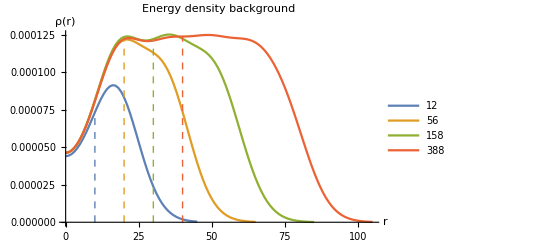

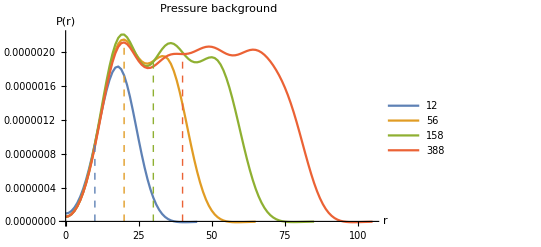

```mathematica
(*Λ = -0.01 energy density and pressure background from surrounding balls*)

ρneg20f = Interpolation[ρneg20];
ρneg40f = Interpolation[ρneg40];
ρneg60f = Interpolation[ρneg60];
ρneg80f = Interpolation[ρneg80];
Pneg20p = Interpolation[Pneg20];
Pneg40p = Interpolation[Pneg40];
Pneg60p = Interpolation[Pneg60];
Pneg80p = Interpolation[Pneg80];

u = a40f[20]-0.000003;
u2 = a40p[20]-0.000000025;

line11=Line[{{10,0},{10,ρneg20f[10]}}];
line21=Line[{{20,0},{20,ρneg40f[20]}}];
line31=Line[{{30,0},{30,ρneg60f[30]}}];
line41=Line[{{40,0},{40,ρneg80f[40]}}];

line51=Line[{{10,0},{10,Pneg20p[10]}}];
line61=Line[{{20,0},{20,Pneg40p[20]}}];
line71=Line[{{30,0},{30,Pneg60p[30]}}];
line81=Line[{{40,0},{40,Pneg80p[40]}}];



ListLinePlot[{ρneg20[[;;-55]], ρneg40[[;;-55]],ρneg60[[;;-55]],ρneg80[[;;-55]]},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},AxesLabel->{Style["r",15],Style["ρ(r)",15]},PlotLabel->Row[Style[#,17]&/@{"Energy density background"}],
PlotLegends->Placed[LineLegend[Style[#,#,#,16]&/@{"12","56","158","388"}],Below],
Epilog->{{Directive[lineStyle1],line11},{Directive[lineStyle2],line21},{Directive[lineStyle3],line31},{Directive[lineStyle4],line41}},TicksStyle->Directive[FontSize->14],ImageSize->{Automatic,280}]

ListLinePlot[{Pneg20[[;;-55]], Pneg40[[;;-55]],Pneg60[[;;-55]],Pneg80[[;;-55]]},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},AxesLabel->{Style["r",15],Style["P(r)",15]},PlotLabel->Row[Style[#,17]&/@{"Pressure background"}],
PlotLegends->Placed[LineLegend[Style[#,#,#,16]&/@{"12","56","158","388"}],Below],Epilog->{{Directive[lineStyle1],line51},{Directive[lineStyle2],line61},{Directive[lineStyle3],line71},{Directive[lineStyle4],line81}},TicksStyle->Directive[FontSize->14],ImageSize->{Automatic,280}]
```

0.

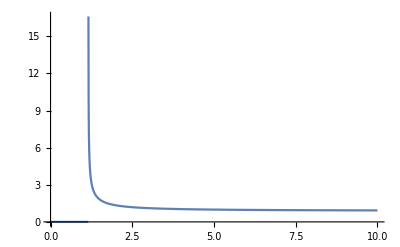

```mathematica
M = 0.5780500506451117;
c = 0.8704346945382065;
A[r_]=Re[c/Sqrt[1-2M/r-0.00015/3r^2]];
A[1]
Plot[A[r],{r,0,10},PlotRange->All]
```

```mathematica
A[r_]=1/Sqrt[1-2*0.5780500506451117/r-0.1r^2]
N[A[2.000000001]]
```

1/(√(1-1.1561/r-0.1 r^2))

6.74968

```mathematica
(*Export["α0gamma.wl",α0gamma];
Export["β0gamma.wl",β0gamma];*)
(*Export["αposgamma.wl",αposgamma];
Export["βposgamma.wl",βposgamma];*)
(*SystemOpen["αposgamma.wl"]
SystemOpen["βposgamma.wl"]
SystemOpen["α0gamma.wl"]
SystemOpen["β0gamma.wl"]*)
(*Import["αposgamma.wl","αposgamma"]*)
```

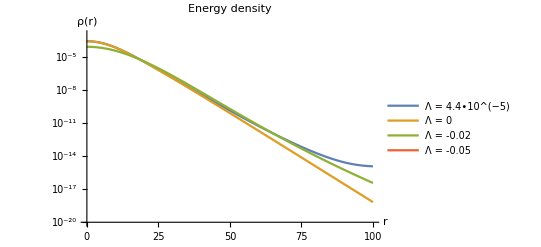

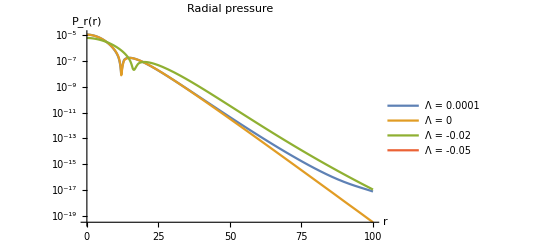

```mathematica
(*graphs to compare pressures from central soliton with different gammas*)

(*Plot[{Interpolation[ρfsy][x],Interpolation[ρposgamma][x],Interpolation[ρlist][x]},{x,0,100},PlotRange->{{0,25},All},AxesLabel->{r,"ρ(r)"},PlotLabel->Style["Energy density",12.4],PlotLegends->Placed[{"Λ = 0","Λ = 0.0001","Λ = -10"},{0.85,0.85}]]

Plot[{Interpolation[Prfsy][x],Interpolation[Prposgamma][x],Interpolation[Prlist][x]},{x,0,100},PlotRange->{{0,30},All},AxesLabel->{r,"Pr(r)"},PlotLabel->Style["Radial pressure",12.4],PlotLegends->Placed[{"Λ = 0","Λ = 0.0001","Λ = -10"},{0.85,0.85}]]*)

Plot[{Interpolation[ρposgamma][x],Interpolation[ρfsy][x],Interpolation[ρneglam2][x],Interpolation[ρlist][x]},{x,0,100},PlotRange->{{0,100},{10^-20,10^-3}},ScalingFunctions->{None,"Log"},AxesLabel->{Style["r",14],Style["ρ(r)",14]},PlotLabel->Row[Style[#,15.5]&/@{"Energy density"}],BaseStyle->{FontSize->13,FontFamily->"Helvetica"},PlotLegends->Placed[{"Λ = 4.4∙10^(−5)","Λ = 0","Λ = -0.02","Λ = -0.05"},{0.2,0.34}],TicksStyle->Directive[FontSize->13],ImageSize->{Automatic,280}]

Plot[{Interpolation[Abs[Prposgamma]][x],Interpolation[Abs[Prfsy]][x],Interpolation[Abs[Prneglam2]][x],Interpolation[Abs[Prlist]][x]},{x,0,100},PlotRange->All,ScalingFunctions->{None,"Log"},AxesLabel->{Style["r",14],Style["P_r(r)",14]},PlotLabel->Row[Style[#,15.5]&/@{"Radial pressure"}],BaseStyle->{FontSize->13,FontFamily->"Helvetica"},PlotLegends->Placed[{"Λ = 0.0001","Λ = 0","Λ = -0.02","Λ = -0.05"},{0.2,0.405}],TicksStyle->Directive[FontSize->13],ImageSize->{Automatic,280}]
```

```mathematica
Export["alpha_list_lam=-0.05.wl",αlist];
SystemOpen["alpha_list_lam=-0.05.wl"]
```

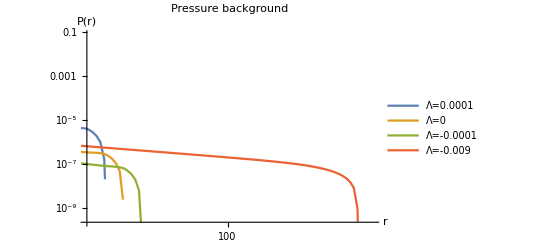

```mathematica
LogLogPlot[{Interpolation[αlistpos1][x],Interpolation[αlistfsy][x],Interpolation[αlistneg1][x],Interpolation[αlistneg3][x]},{x,0,400},PlotRange->{{92,109},All},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},PlotStyle->{{Dashing[{}],Large},{Dashing[{}]},{Dashing[{}]},{Dashing[{}]}},AxesLabel->{r,"P(r)"},PlotLabel->Style["Pressure background",12.4],PlotLegends->Placed[{"Λ=0.0001","Λ=0","Λ=-0.0001","Λ=-0.009"},Below]]
```

```mathematica
αlistneg1
αlistneg2
```

{{1/100000,1.35901×10^-7},{100001/100000,0.013503},{200001/100000,0.0264931},{300001/100000,0.0384936},{400001/100000,0.049097},{500001/100000,0.0579915},{600001/100000,0.0649791},{700001/100000,0.0699815},{800001/100000,0.073035},{900001/100000,0.0742736},{1000001/100000,0.0739056},{1100001/100000,0.0721853},{1200001/100000,0.0693867},{1300001/100000,0.0657806},{1400001/100000,0.0616172},{1500001/100000,0.0571164},{1600001/100000,0.0524621},{1700001/100000,0.0478015},{1800001/100000,0.0432478},{1900001/100000,0.0388834},{2000001/100000,0.0347651},{2100001/100000,0.0309282},{2200001/100000,0.0273917},{2300001/100000,0.0241613},{2400001/100000,0.0212334},{2500001/100000,0.0185975},{2600001/100000,0.0162384},{2700001/100000,0.0141381},{2800001/100000,0.0122768},{2900001/100000,0.0106342},{3000001/100000,0.00919014},{3100001/100000,0.0079249},{3200001/100000,0.00681984},{3300001/100000,0.00585751},{3400001/100000,0.00502172},{3500001/100000,0.00429762},{3600001/100000,0.00367178},{3700001/100000,0.00313206},{3800001/100000,0.00266755},{3900001/100000,0.00226856},{4000001/100000,0.00192649},{4100001/100000,0.00163375},{4200001/100000,0.00138362},{4300001/100000,0.00117028},{4400001/100000,0.00098858},{4500001/100000,0.00083406},{4600001/100000,0.000702858},{4700001/100000,0.000591593},{4800001/100000,0.000497373},{4900001/100000,0.000417695},{5000001/100000,0.000350389},{5100001/100000,0.000293617},{5200001/100000,0.000245781},{5300001/100000,0.000205524},{5400001/100000,0.000171685},{5500001/100000,0.000143273},{5600001/100000,0.000119443},{5700001/100000,0.0000994772},{5800001/100000,0.0000827727},{5900001/100000,0.0000688041},{6000001/100000,0.0000571417},{6100001/100000,0.0000474082},{6200001/100000,0.0000392989},{6300001/100000,0.0000325444},{6400001/100000,0.0000269286},{6500001/100000,0.0000222599},{6600001/100000,0.0000183857},{6700001/100000,0.000015171},{6800001/100000,0.0000125084},{6900001/100000,0.0000103034},{7000001/100000,8.481×10^-6},{7100001/100000,6.97346×10^-6},{7200001/100000,5.72967×10^-6},{7300001/100000,4.70299×10^-6},{7400001/100000,3.85737×10^-6},{7500001/100000,3.16112×10^-6},{7600001/100000,2.58852×10^-6},{7700001/100000,2.11795×10^-6},{7800001/100000,1.73119×10^-6},{7900001/100000,1.41408×10^-6},{8000001/100000,1.15391×10^-6},{8100001/100000,9.41066×10^-7},{8200001/100000,7.66793×10^-7},{8300001/100000,6.24517×10^-7},{8400001/100000,5.0815×10^-7},{8500001/100000,4.12621×10^-7},{8600001/100000,3.34783×10^-7},{8700001/100000,2.71607×10^-7},{8800001/100000,2.20194×10^-7},{8900001/100000,1.78696×10^-7},{9000001/100000,1.45213×10^-7},{9100001/100000,1.18058×10^-7},{9200001/100000,9.60047×10^-8},{9300001/100000,7.79654×10^-8},{9400001/100000,6.33303×10^-8},{9500001/100000,0.},{9600001/100000,0.},{9700001/100000,0.},{9800001/100000,0.},{9900001/100000,0.}}

{{1/100000,1.32605×10^-7},{100001/100000,0.0131806},{200001/100000,0.0258902},{300001/100000,0.037689},{400001/100000,0.0481958},{500001/100000,0.0571122},{600001/100000,0.0642385},{700001/100000,0.0694806},{800001/100000,0.0728477},{900001/100000,0.0744405},{1000001/100000,0.0744321},{1100001/100000,0.0730451},{1200001/100000,0.0705283},{1300001/100000,0.0671359},{1400001/100000,0.0631103},{1500001/100000,0.0586712},{1600001/100000,0.054008},{1700001/100000,0.049278},{1800001/100000,0.0446061},{1900001/100000,0.0400876},{2000001/100000,0.0357916},{2100001/100000,0.0317647},{2200001/100000,0.0280354},{2300001/100000,0.0246173},{2400001/100000,0.0215128},{2500001/100000,0.0187157},{2600001/100000,0.0162136},{2700001/100000,0.01399},{2800001/100000,0.0120256},{2900001/100000,0.0102996},{3000001/100000,0.0087908},{3100001/100000,0.0074781},{3200001/100000,0.00634106},{3300001/100000,0.00536032},{3400001/100000,0.00451777},{3500001/100000,0.00379663},{3600001/100000,0.00318169},{3700001/100000,0.00265911},{3800001/100000,0.00221646},{3900001/100000,0.00184276},{4000001/100000,0.00152824},{4100001/100000,0.00126428},{4200001/100000,0.00104343},{4300001/100000,0.000859167},{4400001/100000,0.000705822},{4500001/100000,0.000578581},{4600001/100000,0.000473233},{4700001/100000,0.000386258},{4800001/100000,0.000314617},{4900001/100000,0.000255739},{5000001/100000,0.000207478},{5100001/100000,0.000167991},{5200001/100000,0.000135767},{5300001/100000,0.000109523},{5400001/100000,0.0000881894},{5500001/100000,0.0000708903},{5600001/100000,0.0000568848},{5700001/100000,0.0000455697},{5800001/100000,0.0000364456},{5900001/100000,0.0000291017},{6000001/100000,0.0000232014},{6100001/100000,0.0000184692},{6200001/100000,0.0000146803},{6300001/100000,0.0000116518},{6400001/100000,9.23493×10^-6},{6500001/100000,7.30941×10^-6},{6600001/100000,5.77729×10^-6},{6700001/100000,4.56044×10^-6},{6800001/100000,3.59544×10^-6},{6900001/100000,2.83116×10^-6},{7000001/100000,2.22659×10^-6},{7100001/100000,1.74774×10^-6},{7200001/100000,1.36937×10^-6},{7300001/100000,1.07363×10^-6},{7400001/100000,8.41112×10^-7},{7500001/100000,6.59629×10^-7},{7600001/100000,5.18888×10^-7},{7700001/100000,4.0831×10^-7},{7800001/100000,3.21409×10^-7},{7900001/100000,2.52133×10^-7},{8000001/100000,1.97051×10^-7},{8100001/100000,0.},{8200001/100000,0.},{8300001/100000,0.},{8400001/100000,0.},{8500001/100000,0.},{8600001/100000,0.},{8700001/100000,0.},{8800001/100000,0.},{8900001/100000,0.},{9000001/100000,0.},{9100001/100000,0.},{9200001/100000,0.},{9300001/100000,0.},{9400001/100000,0.},{9500001/100000,0.},{9600001/100000,0.},{9700001/100000,0.},{9800001/100000,0.},{9900001/100000,0.}}

```mathematica
Manipulate[Plot[1-W/3r^2 - 2/r,{r,-100,100},PlotRange->{{-10,10},{-10,10}}],{W,-100,100}]
```